```mathematica
Quit
```

## Data

```mathematica
SetDirectory[NotebookDirectory[]];
Get["g20"];
```

```mathematica
mutilde=10;
bSub=10^-5;
```

```mathematica
background=newton[initguess[1/mutilde],abc/.{b0->bSub,temp->1/mutilde},abc2/.{b0->bSub,temp->1/mutilde}]
```

start norm: 8.180×10^-4

iteration: 1 norm: 1.390×10^-9		 T subt: 1.607  T solve: 1.2636

iteration: 2 norm: 0.×10^-20		 T subt: 1.186  T solve: 0.624001

overall time: 4.92961

{-1.94312266155280005253413814276465099908333858910630029842266,-1.94307880303752749211277839080204008988576098988028662774093,-1.94243046344296793426487091796488074424233230360533393233942,-1.93969757564479245537145872720956334204812430633231880821818,-1.93263944650020246127573828922814034761521642757394988313418,-1.918566769207539544638708871180739419193429535717883977362,-1.89472727203344453289094103460326237012757901062939146925239,-1.85872064229149752036094132067643383605779653417718188289417,-1.80889457959582818269592799744145879583741753758495427272058,-1.74467535172734924438746534308699836574547111018282880691502,-1.66679289963536313349879057121586522008597714889420282764425,-1.5773716535886980803099788791481203106914825826856367073202,-1.47987258425589957466661968603237418112364387930403747735536,-1.37888806940996843774962589138982930024102629002065732966211,-1.27980717075183997696872539598066051917715729962802072908975,-1.18838314893651322687028360697460154598911493132025212930404,-1.11024595063940763775486803136922532187973978596509339035903,-1.05040878910691443982611233617881945340810142665479840872669,-1.01281910531944698134066174696045831432765490847489757089175,-1.,3.9950483316590553043888412128033996750401339887272496372019×10^-12,3.9944635028802931624471446178224069797725632165942894057142×10^-12,3.985809828535092298952022602190448095628603944196301013395×10^-12,3.9492414965065872035839448806141156817785134269394123519796×10^-12,3.8545218596202233863483419516256971127597737701209511873233×10^-12,3.6657630088101348529171260259088150420147606869035033811441×10^-12,3.3490584770538429433208910053970474403471882106583007272465×10^-12,2.882308132294961055846525965577079276679566966546261760016×10^-12,2.2640264770310978313099694491643319749320657915277414218361×10^-12,1.5169119490187352387967406470273183957236356167648817521373×10^-12,6.8418263762316122478736827281223962050502421745275139185216×10^-13,-1.794821668523707335310016240632535358407186488828748185831×10^-13,-1.0184176402386262891752667326777064220129714175257288773326×10^-12,-1.784556551972934651369399684098692326727236138652930243132×10^-12,-2.4427503801167371142629253408014872700961562863733346365123×10^-12,-2.9729048904386974983216908892029253441792526874689766298717×10^-12,-3.3694273767875333617185381988268756201242427515307221548478×10^-12,-3.6382639645793417587240745676716600586332719834572039859729×10^-12,-3.791636202214155084131946110467480845104084113122583376024×10^-12,-3.8411767300167405415193160316825262242566673099703429276257×10^-12,-1.9975241658045985458705967265505286628780793722104246826685×10^-12,-1.997377939213206745499295897979273181486235247064756368343×10^-12,-1.9952104283302764763452874572648090333491397481723620401998×10^-12,-1.9859934507939204751912452918041528874981918653661544688144×10^-12,-1.9617937454524890058671867940018922507653460520080374948071×10^-12,-1.9125132539710330985927543659211063247392307266011569997023×10^-12,-1.8274400675902240950521791506152987859152411442379901657463×10^-12,-1.6978642883701729278528720898252003921161471418065772947371×10^-12,-1.5201259017225218074959338785434327281884083391739910835629×10^-12,-1.2977042398954782085868446497612270335520662224267498124297×10^-12,-1.0412262552534944104510949975070938118609430905236232082817×10^-12,-7.664271840686140090610333177664601860910008070605301316833×10^-13,-4.9107990850130126993696760373503878547490555670065180334465×10^-13,-2.320365836795559452801415250307386500378169925708203853117×10^-13,-3.04627608994782573362856063627950070829417486395420019949×10^-15,1.864902467137723575118399792453288897544487549082005734943×10^-13,3.3188521538168780604889265499948149643002577059692996857749×10^-13,4.3266371029011319937035889531210128262713401195815477014543×10^-13,4.9113717540779901090790102479926825317219808138672306636551×10^-13,5.102011133445241893914786444762554007122603040597024449521×10^-13,4.08384091892633592200185672912199732212540660543875547148611×10^-6,4.11162631802270876112815931811212062769732278067785379617774×10^-6,4.1934520089900122280520311422920585187108438753156203097881×10^-6,4.32471380878834012892714748245156248828437996849699881337496×10^-6,4.49776469114310030834160383573257480779576388233824512649131×10^-6,4.70216636300370440810363376391561766040288917135640470576386×10^-6,4.925353810832427802199668313625978478963895118211930102355×10^-6,5.15377587340253599112099825154615101060174515348325952343438×10^-6,5.37433531521940447130103098899618855480245224398873904077347×10^-6,5.57575846086406187071027333465729314158035133838437882557261×10^-6,5.74954442927049419328366822573509517703099547664373399369332×10^-6,5.89037034775418652350348021808655335440670705947667531040528×10^-6,5.99607482238737544238745761620217728079774493813638444069169×10^-6,6.06743951339491566478709556479845431990618355671797408019101×10^-6,6.10792387902667168469171035575492654591269620369054075922899×10^-6,6.1233647424037260722483600715093020101844706772087854438036×10^-6,6.12150855866077136020061011016484954181265023630837145734793×10^-6,6.11115594589517796134165596573899705344444639520814731785494×10^-6,6.1007471926640313873304013034029891110379381806778234715627×10^-6,6.09650758755706255713225017558426079554036954995218470496713×10^-6,1.68207252656906792316475261873187927851710365360651823884986,1.69354316499131291818985219009763765311356838941658609464886,1.72764219114360122905040766763273802646148104481729240058741,1.78343947248199315214451173586543015721762654759510778589795,1.85941300462417876969131194266291174502211865132678073777786,1.95349042766145863970699258317873133530602726615416621488281,2.06310555473481902341924227365468014848231259312226586013668,2.18526837092290595120412550282771264338403134914660048837207,2.31664659305470504474162999904378950761246070649195548588641,2.45365656570784324064173975756394913290485774056815518815034,2.59256101398662447431454732558937857106930399538150237638893,2.72957098663883935302353470441444545662554686414489439861657,2.86094920876887319385401501646208444334010663334979872579956,2.9831120249545210296922996545161240265062972577188992466399,3.09272715202502278663425490617807815390962400261142325839216,3.18680457505934495000073246635445404834329534266613360950014,3.26277810719881625318700365717302160281229200134009521073934,3.31857538853504512459744922342374999511467695540652551248403,3.35267441468594913729059262902790611423159931387020403650767,3.36414505310771902921344054192784761417616057452836710539242,-9.71145026012089092983967490726585782125984581490663269556727×10^-6,-9.71122446050555622105711615106237157828245225351500905892731×10^-6,-9.70788858853975573159619745300777397039254729322206484317317×10^-6,-9.69386853008579573172166037613350282568976011484480003028556×10^-6,-9.65796465158452327763423315865674554118089381513581385197277×10^-6,-9.58765398248750319327041663003452397906363827861694073006698×10^-6,-9.47221750201071514875099406803940204872286489275802988045464×10^-6,-9.30589215597529602973301607696567743300834371555657938527584×10^-6,-9.08980984127615104569074345870582411652667908185724816401003×10^-6,-8.83183425804791425115073839810332090490318757162229758885081×10^-6,-8.54449946026403665059789558609695538378524265422846844494999×10^-6,-8.24221439735328077829928415021501641648862626290938930598951×10^-6,-7.93897576154562081191853856260701811158649275819150694296898×10^-6,-7.64719531224993592199673660100690327824765542812698048368403×10^-6,-7.3775619956877047022096348273952528581556408235576080961854×10^-6,-7.13950774475980980938178493743722744922781176942204904188706×10^-6,-6.94178150196888213747393866420066966888508234299946918502966×10^-6,-6.79268187729194433133277076081915625441074544102874654622406×10^-6,-6.69961143515051094134080508087266745077471463823027772392676×10^-6,-6.66792629594914964769155762739915087732644129077052306083988×10^-6}

## Loading things

### Matrix

```mathematica
firstTotal=({{-(u[z] w[z])/(2 z), 0, 0, 0, 0, 0, 0, 0}, {0, -(u[z] w[z])/(2 z), 0, 0, 0, 0, 0, 0}, {0, 0, w[z]/(2 z^3), 0, -(c[z] w[z])/(2 z^3), 0, 0, 0}, {0, 0, 0, w[z]/(2 z^3), 0, -(c[z] w[z])/(2 z^3), 0, 0}, {0, 0, -(c[z] w[z])/(2 z^3), 0, (u[z]-c[z]^2 w[z]^2)/(2 z^3 w[z])+(-u[z]+c[z]^2 w[z]^2)/(z^3 w[z]), 0, 0, 0}, {0, 0, 0, -(c[z] w[z])/(2 z^3), 0, (u[z]-c[z]^2 w[z]^2)/(2 z^3 w[z])+(-u[z]+c[z]^2 w[z]^2)/(z^3 w[z]), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});
```

```mathematica
secondBulk=({{-(ⅈ (ω+k c[z]) w[z])/(2 z), -1/6 ⅈ γ (k AV[z]+ω P[z]), -(w[z] (AV'[z]-c[z] P'[z]))/(2 z), (B w[z])/(2 z vv[z]^2), (c[z] w[z]^2 AV'[z]+u[z] P'[z]-c[z]^2 w[z]^2 P'[z])/(2 z w[z]), -(B c[z] w[z])/(2 z vv[z]^2), 0, -(B u[z] w[z])/(2 z vv[z]^2)}, {1/6 ⅈ γ (k AV[z]+ω P[z]), -(ⅈ (ω+k c[z]) w[z])/(2 z), -(B w[z])/(2 z vv[z]^2), -(w[z] (AV'[z]-c[z] P'[z]))/(2 z), (B c[z] w[z])/(2 z vv[z]^2), (c[z] w[z]^2 AV'[z]+u[z] P'[z]-c[z]^2 w[z]^2 P'[z])/(2 z w[z]), (B u[z] w[z])/(2 z vv[z]^2), 0}, {0, 0, (z w[z] vv'[z]+vv[z] (-3 w[z]+z w'[z]))/(z^4 vv[z]), 0, -(z vv[z] w[z] c'[z]+2 c[z] (z w[z] vv'[z]+vv[z] (-3 w[z]+z w'[z])))/(2 z^4 vv[z]), 0, (ⅈ (ω+k c[z]) w[z])/(2 z^3), 0}, {0, 0, 0, (z w[z] vv'[z]+vv[z] (-3 w[z]+z w'[z]))/(z^4 vv[z]), 0, -(z vv[z] w[z] c'[z]+2 c[z] (z w[z] vv'[z]+vv[z] (-3 w[z]+z w'[z])))/(2 z^4 vv[z]), 0, (ⅈ (ω+k c[z]) w[z])/(2 z^3)}, {0, 0, (-2 z c[z] w[z]^2 vv'[z]+vv[z] (-ⅈ k z-z w[z]^2 c'[z]+2 c[z] w[z] (3 w[z]-z w'[z])))/(2 z^4 vv[z] w[z]), 0, (-2 z (u[z]-c[z]^2 w[z]^2) vv'[z]+vv[z] (-ⅈ z ω+6 u[z]+2 z c[z] w[z]^2 c'[z]-z u'[z]+2 c[z]^2 w[z] (-3 w[z]+z w'[z])))/(2 z^4 vv[z] w[z]), 0, -(ⅈ (-k u[z]+c[z] (ω+k c[z]) w[z]^2))/(2 z^3 w[z]), 0}, {0, 0, 0, (-2 z c[z] w[z]^2 vv'[z]+vv[z] (-ⅈ k z-z w[z]^2 c'[z]+2 c[z] w[z] (3 w[z]-z w'[z])))/(2 z^4 vv[z] w[z]), 0, (-2 z (u[z]-c[z]^2 w[z]^2) vv'[z]+vv[z] (-ⅈ z ω+6 u[z]+2 z c[z] w[z]^2 c'[z]-z u'[z]+2 c[z]^2 w[z] (-3 w[z]+z w'[z])))/(2 z^4 vv[z] w[z]), 0, -(ⅈ (-k u[z]+c[z] (ω+k c[z]) w[z]^2))/(2 z^3 w[z])}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});
```

```mathematica
secondCounter=({{-(Log[z] (-k^2 u[z]+(ω+k c[z])^2 w[z]^2))/(2 √u[z] w[z]), 0, 0, -(ⅈ B (ω+k c[z]) Log[z] w[z])/(2 √u[z] vv[z]^2), 0, -(ⅈ B Log[z] (k u[z]-c[z] (ω+k c[z]) w[z]^2))/(2 √u[z] vv[z]^2 w[z]), 0, 0}, {0, -(Log[z] (-k^2 u[z]+(ω+k c[z])^2 w[z]^2))/(2 √u[z] w[z]), (ⅈ B (ω+k c[z]) Log[z] w[z])/(2 √u[z] vv[z]^2), 0, -(ⅈ B Log[z] (-k u[z]+c[z] (ω+k c[z]) w[z]^2))/(2 √u[z] vv[z]^2 w[z]), 0, 0, 0}, {0, -(ⅈ B (ω+k c[z]) Log[z] w[z])/(2 √u[z] vv[z]^2), (-2 k^2 z^4 (ω+k c[z])^2 Log[z] vv[z]^4 w[z]^2+u[z] (-4 B^2 z^4 Log[z] w[z]^4+vv[z]^4 (2 k^4 z^4 Log[z]+4 k^2 z^2 w[z]^2+48 w[z]^4)))/(16 z^4 u[z]^(3/2) vv[z]^4 w[z]^3), 0, (-2 k z^4 ω (ω+k c[z])^2 Log[z] vv[z]^4 w[z]^2+u[z] (4 B^2 z^4 c[z] Log[z] w[z]^4+vv[z]^4 (2 k^3 z^4 ω Log[z]+4 k z^2 ω w[z]^2-48 c[z] w[z]^4)))/(16 z^4 u[z]^(3/2) vv[z]^4 w[z]^3), 0, 0, 0}, {(ⅈ B (ω+k c[z]) Log[z] w[z])/(2 √u[z] vv[z]^2), 0, 0, (-2 k^2 z^4 (ω+k c[z])^2 Log[z] vv[z]^4 w[z]^2+u[z] (-4 B^2 z^4 Log[z] w[z]^4+vv[z]^4 (2 k^4 z^4 Log[z]+4 k^2 z^2 w[z]^2+48 w[z]^4)))/(16 z^4 u[z]^(3/2) vv[z]^4 w[z]^3), 0, (-2 k z^4 ω (ω+k c[z])^2 Log[z] vv[z]^4 w[z]^2+u[z] (4 B^2 z^4 c[z] Log[z] w[z]^4+vv[z]^4 (2 k^3 z^4 ω Log[z]+4 k z^2 ω w[z]^2-48 c[z] w[z]^4)))/(16 z^4 u[z]^(3/2) vv[z]^4 w[z]^3), 0, 0}, {0, -(ⅈ B Log[z] (k u[z]-c[z] (ω+k c[z]) w[z]^2))/(2 √u[z] vv[z]^2 w[z]), (-2 k z^4 ω (ω+k c[z])^2 Log[z] vv[z]^4 w[z]^2+u[z] (4 B^2 z^4 c[z] Log[z] w[z]^4+vv[z]^4 (2 k^3 z^4 ω Log[z]+4 k z^2 ω w[z]^2-48 c[z] w[z]^4)))/(16 z^4 u[z]^(3/2) vv[z]^4 w[z]^3), 0, (-2 z^4 ω^2 (ω+k c[z])^2 Log[z] vv[z]^4 w[z]^2-2 u[z]^2 (-2 B^2 z^4 Log[z]+24 vv[z]^4) w[z]^2+u[z] (-4 B^2 z^4 c[z]^2 Log[z] w[z]^4+vv[z]^4 (2 k^2 z^4 ω^2 Log[z]+4 z^2 ω^2 w[z]^2+48 c[z]^2 w[z]^4)))/(16 z^4 u[z]^(3/2) vv[z]^4 w[z]^3), 0, 0, 0}, {-(ⅈ B Log[z] (-k u[z]+c[z] (ω+k c[z]) w[z]^2))/(2 √u[z] vv[z]^2 w[z]), 0, 0, (-2 k z^4 ω (ω+k c[z])^2 Log[z] vv[z]^4 w[z]^2+u[z] (4 B^2 z^4 c[z] Log[z] w[z]^4+vv[z]^4 (2 k^3 z^4 ω Log[z]+4 k z^2 ω w[z]^2-48 c[z] w[z]^4)))/(16 z^4 u[z]^(3/2) vv[z]^4 w[z]^3), 0, (-2 z^4 ω^2 (ω+k c[z])^2 Log[z] vv[z]^4 w[z]^2-2 u[z]^2 (-2 B^2 z^4 Log[z]+24 vv[z]^4) w[z]^2+u[z] (-4 B^2 z^4 c[z]^2 Log[z] w[z]^4+vv[z]^4 (2 k^2 z^4 ω^2 Log[z]+4 z^2 ω^2 w[z]^2+48 c[z]^2 w[z]^4)))/(16 z^4 u[z]^(3/2) vv[z]^4 w[z]^3), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});
```

### Hard coded equations

```mathematica
vectorAFinal={B hV2[z] w[z]^2+2 ⅈ z ω w[z]^2 a1'[z]+2 ⅈ k z c[z] w[z]^2 a1'[z]-u[z] w[z]^2 a1'[z]-ⅈ k z^2 γ a2[z] w[z] AV'[z]+B z^2 γ h13[z] w[z] AV'[z]-z c[z] vv[z]^2 w[z]^2 AV'[z] h13'[z]+B z c[z] w[z]^2 h23'[z]+z vv[z]^2 w[z]^2 AV'[z] hV1'[z]-B z w[z]^2 hV2'[z]-ⅈ z ω h13[z] vv[z]^2 P'[z]-ⅈ k z hV1[z] vv[z]^2 P'[z]-ⅈ z^2 γ ω a2[z] w[z] P'[z]-B z^2 γ hV1[z] w[z] P'[z]-z u[z] vv[z]^2 h13'[z] P'[z]+z c[z]^2 vv[z]^2 w[z]^2 h13'[z] P'[z]-z c[z] vv[z]^2 w[z]^2 hV1'[z] P'[z]+z w[z]^2 a1'[z] u'[z]-B z hV2[z] w[z] w'[z]+z u[z] w[z] a1'[z] w'[z]+a1[z] (-k^2 z-ⅈ w[z]^2 (ω+k c[z]-k z c'[z])+ⅈ z (ω+k c[z]) w[z] w'[z])+B h23[z] (z (ⅈ k+w[z]^2 c'[z])+c[z] w[z] (-w[z]+z w'[z]))+z u[z] w[z]^2 a1''[z],-B hV1[z] w[z]^2+2 ⅈ z ω w[z]^2 a2'[z]+2 ⅈ k z c[z] w[z]^2 a2'[z]-u[z] w[z]^2 a2'[z]+ⅈ k z^2 γ a1[z] w[z] AV'[z]+B z^2 γ h23[z] w[z] AV'[z]-B z c[z] w[z]^2 h13'[z]-z c[z] vv[z]^2 w[z]^2 AV'[z] h23'[z]+B z w[z]^2 hV1'[z]+z vv[z]^2 w[z]^2 AV'[z] hV2'[z]-ⅈ z ω h23[z] vv[z]^2 P'[z]-ⅈ k z hV2[z] vv[z]^2 P'[z]+ⅈ z^2 γ ω a1[z] w[z] P'[z]-B z^2 γ hV2[z] w[z] P'[z]-z u[z] vv[z]^2 h23'[z] P'[z]+z c[z]^2 vv[z]^2 w[z]^2 h23'[z] P'[z]-z c[z] vv[z]^2 w[z]^2 hV2'[z] P'[z]+z w[z]^2 a2'[z] u'[z]+B z hV1[z] w[z] w'[z]+z u[z] w[z] a2'[z] w'[z]+a2[z] (-k^2 z-ⅈ w[z]^2 (ω+k c[z]-k z c'[z])+ⅈ z (ω+k c[z]) w[z] w'[z])+B h13[z] (-ⅈ k z-z w[z]^2 c'[z]+c[z] w[z] (w[z]-z w'[z]))+z u[z] w[z]^2 a2''[z],ⅈ B z^3 ω a2[z] w[z]^2+B^2 z^3 hV1[z] w[z]^2+z^3 vv[z]^2 w[z]^2 (-ⅈ a1[z] (ω+k c[z])-B c[z] h23[z]+B hV2[z]-u[z] a1'[z]) AV'[z]-4 ⅈ z vv[z]^3 w[z]^2 (c[z] (ω h13[z]+k hV1[z])-ⅈ u[z] hV1'[z]) vv'[z]+vv[z]^4 (ω h13[z] (k z+ⅈ c[z] w[z] (3 w[z]+z w'[z]))+k hV1[z] (k z+ⅈ c[z] w[z] (3 w[z]+z w'[z]))+w[z] (z c[z]^2 w[z]^3 c'[z] h13'[z]-ⅈ z ω w[z] hV1'[z]+z c[z] (-w[z]^3 c'[z] hV1'[z]-ⅈ w[z] (2 k hV1'[z]+h13'[z] (ω-ⅈ u'[z]))+2 u[z] h13'[z] w'[z])+u[z] (-z hV1'[z] w'[z]+w[z] (z c'[z] h13'[z]+3 hV1'[z]-z hV1''[z])))),-ⅈ B z^3 ω a1[z] w[z]^2+B^2 z^3 hV2[z] w[z]^2+z^3 vv[z]^2 w[z]^2 (-ⅈ a2[z] (ω+k c[z])+B c[z] h13[z]-B hV1[z]-u[z] a2'[z]) AV'[z]-4 ⅈ z vv[z]^3 w[z]^2 (c[z] (ω h23[z]+k hV2[z])-ⅈ u[z] hV2'[z]) vv'[z]+vv[z]^4 (ω h23[z] (k z+ⅈ c[z] w[z] (3 w[z]+z w'[z]))+k hV2[z] (k z+ⅈ c[z] w[z] (3 w[z]+z w'[z]))+w[z] (z c[z]^2 w[z]^3 c'[z] h23'[z]-ⅈ z ω w[z] hV2'[z]+z c[z] (-w[z]^3 c'[z] hV2'[z]-ⅈ w[z] (2 k hV2'[z]+h23'[z] (ω-ⅈ u'[z]))+2 u[z] h23'[z] w'[z])+u[z] (-z hV2'[z] w'[z]+w[z] (z c'[z] h23'[z]+3 hV2'[z]-z hV2''[z])))),-ⅈ B k z^3 a2[z] w[z]+z vv[z]^4 w[z]^3 c'[z] (c[z] h13'[z]-hV1'[z])+z vv[z]^4 (ⅈ ω h13[z]+ⅈ k hV1[z]+u[z] h13'[z]) w'[z]+w[z] (h13[z] (B^2 z^3+3 ⅈ ω vv[z]^4-4 ⅈ z ω vv[z]^3 vv'[z])+vv[z]^2 (z^3 (-ⅈ a1[z] (ω+k c[z])-B c[z] h23[z]+B hV2[z]-u[z] a1'[z]) P'[z]+4 z vv[z] (-ⅈ k hV1[z]-u[z] h13'[z]) vv'[z]-ⅈ vv[z]^2 (-3 k hV1[z]+h13'[z] (2 z ω+k z c[z]+3 ⅈ u[z]-ⅈ z u'[z])+z (k hV1'[z]-ⅈ u[z] h13''[z])))),ⅈ B k z^3 a1[z] w[z]+z vv[z]^4 w[z]^3 c'[z] (c[z] h23'[z]-hV2'[z])+z vv[z]^4 (ⅈ ω h23[z]+ⅈ k hV2[z]+u[z] h23'[z]) w'[z]+w[z] (h23[z] (B^2 z^3+3 ⅈ ω vv[z]^4-4 ⅈ z ω vv[z]^3 vv'[z])+vv[z]^2 (z^3 (-ⅈ a2[z] (ω+k c[z])+B c[z] h13[z]-B hV1[z]-u[z] a2'[z]) P'[z]+4 z vv[z] (-ⅈ k hV2[z]-u[z] h23'[z]) vv'[z]-ⅈ vv[z]^2 (-3 k hV2[z]+h23'[z] (2 z ω+k z c[z]+3 ⅈ u[z]-ⅈ z u'[z])+z (k hV2'[z]-ⅈ u[z] h23''[z])))),-ⅈ B z^2 a2[z] (ω+k c[z]) w[z]^2+B z^2 w[z]^2 (B c[z] h13[z]-B hV1[z]-u[z] a2'[z])-vv[z]^4 (k ω h13[z]+k^2 hV1[z]-ⅈ (k u[z] h13'[z]-(ω+k c[z]) w[z]^2 (c[z] h13'[z]-hV1'[z])))+z^2 vv[z]^2 (ⅈ a1[z] (k u[z] P'[z]+(ω+k c[z]) w[z]^2 (AV'[z]-c[z] P'[z]))+B (-hV2[z] w[z]^2 AV'[z]+h23[z] u[z] P'[z]-c[z]^2 h23[z] w[z]^2 P'[z]+c[z] w[z]^2 (h23[z] AV'[z]+hV2[z] P'[z]))),ⅈ B z^2 a1[z] (ω+k c[z]) w[z]^2+B z^2 w[z]^2 (B c[z] h23[z]-B hV2[z]+u[z] a1'[z])-vv[z]^4 (k ω h23[z]+k^2 hV2[z]-ⅈ (k u[z] h23'[z]-(ω+k c[z]) w[z]^2 (c[z] h23'[z]-hV2'[z])))+z^2 vv[z]^2 (ⅈ a2[z] (k u[z] P'[z]+(ω+k c[z]) w[z]^2 (AV'[z]-c[z] P'[z]))+B (hV1[z] w[z]^2 AV'[z]-h13[z] u[z] P'[z]+c[z]^2 h13[z] w[z]^2 P'[z]-c[z] w[z]^2 (h13[z] AV'[z]+hV1[z] P'[z])))};
```

### Get four term fluctuation expansion here

```mathematica
(* Import the horizon expansion of the background here*)

SetDirectory[NotebookDirectory[]];
Quiet[Get["horExpBack6.m"]];
```

Saved with name “horSeries”, “flucHorSeries”

```mathematica
SetDirectory[NotebookDirectory[]];
Quiet[Get["flucExpSixEqnSystJWtype.m"]];

flucHorSeries=flucHorSeries;
```

```mathematica
subFluc0={c1[0]->(v[0]^4 (av[0] v[0]^2 (ⅈ k c13[0]-cv1[0] w[0]^2)+B (-ⅈ k c23[0]+cv2[0] w[0]^2)))/((B^2+av[0]^2 v[0]^4) w[0]^2),c2[0]->(ⅈ v[0]^4 (B (k c13[0]+ⅈ cv1[0] w[0]^2)+av[0] v[0]^2 (k c23[0]+ⅈ cv2[0] w[0]^2)))/((B^2+av[0]^2 v[0]^4) w[0]^2)};
```

```mathematica
Coefficient[hV1[z]/.flucHorSeries,c1[2]]//Simplify
```

0

### Psub and ruleBDR

```mathematica
functions={{u[z],w[z],vv[z],c[z]},{AV[z],P[z]}}//Flatten;
```

```mathematica
psub={c->((1-#1) #1^4 c[#1]&),
u->(1+1/6 B^2 #1^4 Log[#1]+#1^4 u[#1]&),
vv->(1-1/24 B^2 #1^4 Log[#1]+#1^4 vv[#1]&),w->(1+1/12 B^2 #1^4 Log[#1]+#1^4 w[#1]&),
AV->((1-#1) AV[#1]&),P->(#1^2 P[#1]&)};
```

```mathematica
ruleBDR={u->Function[z,1+z^4 u4+1/6 z^4 Log[z] B^2(*+O[z]^6*)],vv->Function[z,1+1/2 z^4 (-w4)+1/24 z^4 Log[z] (-B^2)(*+O[z]^6*)],w->Function[z,1+z^4 w4+1/12 z^4 Log[z] B^2(*+O[z]^6*)],c->Function[z,z^4 (c4+1/12 z^4 Log[z] (-B^2))(*+O[z]^6*)],P->Function[z,z^2 (p1/2+1/8 (γ B ρ) z^2)(*+O[z]^6*)],AV->Function[z,μ-(ρ z^2)/2-1/8 (γ B p1) z^4(*+O[z]^6*)]};
```

## Background

### Import

```mathematica
(*SetDirectory[NotebookDirectory[]<>"backgrounds"];
backData=Get["back082719γSUSYμT10B1d100"];*)
```

```mathematica
(*γSub=backData⟦1,1⟧;
mutilde=backData⟦1,2⟧
bSub=backData⟦1,3⟧

background=backData⟦2⟧;*)
```

```mathematica
γSub=2/(√3);
μSub=mutilde;
bSub=bSub;
```

```mathematica
prec1=60;
gSize=1/6 Length[background];
zgrid=SetPrecision[Table[1/2 (1-Cos[(n π)/(gSize-1)]),{n,0,gSize-1}],prec1];
{uSub,wSub,vSub,cSub,avSub,pSub}=Interpolation[{zgrid,background⟦gSize #+1;;gSize(#+1)⟧}//Transpose]&/@Range[0,5];

backSub=SetPrecision[{u->uSub,w->wSub,vv->vSub,c->cSub,AV->avSub, P->pSub},prec1];
```

### Check

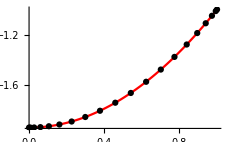
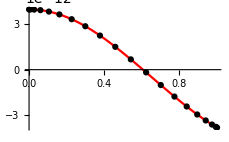
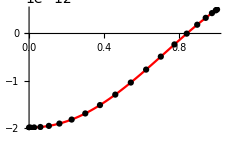
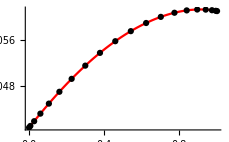
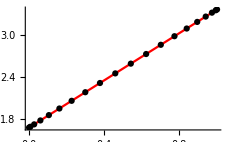
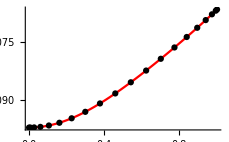

```mathematica
Table[ListPlot[{zgrid,background⟦gSize i+1;;gSize(i+1)⟧}//Transpose,PlotStyle->Black],{i,0,5}];
Plot[backSub⟦#,2⟧[z],{z,0,1},PlotStyle->Red]&/@Range[Length[backSub]];
Show[%⟦#⟧,%%⟦#⟧,ImageSize->230]&/@Range[6]
```

```mathematica
backSub//Precision
backData//Precision
background//Precision
```

60.

∞

57.0639

### Thermodynamics

```mathematica
taap=SetPrecision[1/(4π)Abs[u'[z]/.psub/.backSub/.B->bSub/.z->1],prec1]
entropy=SetPrecision[4π vv[z]^2 w[z]/.psub/.backSub/.B->bSub/.z->1,prec1]
n0=SetPrecision[-D[AV[z]/.psub/.backSub,{z,2}]/.z->0,prec1]
u4=background⟦1⟧;
w4=background⟦68+1⟧;
ϵ0=-3u4
p0=-u4+8w4
w0=ϵ0+p0
```

0.168207252656906914577823657894701489222990517368786201666266

12.5663706143237260560221768478338378377584828245416635388366

3.36414505317527003293087751766980012278612954783888225682705

5.82936798465840015760241442829395299725001576731890089526799

1.94316565623532180776990855101256296859177700872425220833499

7.77253364089372196537232297930651596584179277604315310360298

```mathematica
bSub/taap^2
```

0.00035343582221518070781261009691333335768944706006012150367873

## Green function (ω = 0, k→0)

### Hyperparameter

```mathematica
zBdr=10^-10;
zHor=1-zBdr;

wp=prec1-2; 
pg=21; 
ag=10^2;
```

### Green function

```mathematica
vectorNOω=vectorAFinal/.ω->0//Simplify;
vectorEQN=SetPrecision[vectorNOω/.psub/.backSub/.{B->bSub,γ->γSub}//Simplify,prec1];

{uNot,vNot,wNot,cNot,avNot,pNot}=SetPrecision[{-u'[z],vv[z],w[z],-c'[z],-AV'[z],P[z]}/.psub/.backSub/.B->bSub/.z->zHor,prec1];

ruleUVWCAVP1=SetPrecision[{u[0]->uNot,v[0]->vNot,w[0]->wNot,c[0]->cNot,av[0]->avNot,p[0]->pNot},prec1];

beingSpecific=SetPrecision[{{c1[0]->z1,cv1[0]-> zV1, c13[0]->z13},{c2[0]->z2,cv2[0]-> zV2, c23[0]->z23},{B->bSub,γ->γSub}}//Flatten,prec1];

positionType=SetPrecision[Limit[{a1[z],a2[z],hV1[z],hV2[z],h13[z],h23[z]}/.flucHorSeries/.subFluc0/.beingSpecific/.ruleUVWCAVP1/.z->zHor,ω->0]//Simplify,prec1];

velocityType=SetPrecision[Limit[D[{a1[z],a2[z],hV1[z],hV2[z],h13[z],h23[z]}/.flucHorSeries/.subFluc0/.beingSpecific/.ruleUVWCAVP1,z]/.z->zHor,ω->0]//Simplify,prec1];
```

```mathematica
solSix[momentum_?NumericQ, hv1Zero_?NumericQ,hv2Zero_?NumericQ,h13Zero_?NumericQ,h23Zero_?NumericQ]:=Block[{k=momentum,zV1=hv1Zero,zV2=hv2Zero, z13=h13Zero,z23=h23Zero},NDSolve[{0== vectorEQN⟦1⟧,0== vectorEQN⟦2⟧, 0==vectorEQN⟦3⟧,0== vectorEQN⟦4⟧,0== vectorEQN⟦5⟧, 0==vectorEQN⟦6⟧,a1[zHor]==positionType⟦1⟧,a2[zHor]== positionType⟦2⟧, hV1[zHor]== positionType⟦3⟧,hV2[zHor]==positionType⟦4⟧,h13[zHor]==positionType⟦5⟧, h23[zHor]==positionType⟦6⟧,a1'[zHor]==velocityType⟦1⟧,a2'[zHor]== velocityType⟦2⟧,hV1'[zHor]==velocityType⟦3⟧,hV2'[zHor]==velocityType⟦4⟧,h13'[zHor]== velocityType⟦5⟧,h23'[zHor]==velocityType⟦6⟧},{a1[z],a2[z],hV1[z],hV2[z],h13[z],h23[z]},{z,zBdr,zHor},MaxSteps->2 10^4,WorkingPrecision->wp,PrecisionGoal->pg,AccuracyGoal->ag]]

pureGauge1[ω_,k_,B_]={B,0,0,ⅈ ω,0,-ⅈ k}; 
pureGauge2[ω_,k_,B_]={0,B,-ⅈ ω,0,ⅈ k,0};

hIJ[k_]:=SetPrecision[Transpose[({{pureGauge1[0,k,bSub]}, {pureGauge2[0,k,bSub]}, {solSix[k,1,1,1,-1]⟦1,;;,2⟧}, {solSix[k,1,1,-1,1]⟦1,;;,2⟧}, {solSix[k,1,-1,1,1]⟦1,;;,2⟧}, {solSix[k,-1,1,1,1]⟦1,;;,2⟧}})] ,prec1]

hIJ0[k_]:=SetPrecision[hIJ[k]/.z->zBdr,prec1]
hIJ0I[k_]:=SetPrecision[Inverse[hIJ0[k]],prec1]
fQ[k_]:=SetPrecision[hIJ[k].hIJ0I[k],prec1]
fQp[k_]:=SetPrecision[D[fQ[k],z] ,prec1]

first[k_]=SetPrecision[Table[firstTotal⟦i,j⟧,{i,6},{j,6}]/.{ω->0,B->bSub,γ->γSub}//Simplify,prec1];
second[k_]=SetPrecision[Table[(secondBulk+secondCounter)⟦i,j⟧,{i,6},{j,6}]/.{ω->0,B->bSub,γ->γSub}//Simplify,prec1];

green[k_]:=SetPrecision[-2(first[k].fQp[k]+second[k]),prec1]
```

## Computation

```mathematica
kSub=10^-8;
```

### ω depenednce of M_5

#### ω grid

```mathematica
prec1=60;
ωgSize=50;
ωAxis=SetPrecision[Table[L+ (1-Cos[(n π)/(2ωgSize-1)])(U-L),{n,0,2ωgSize-1}]⟦;;ωgSize⟧/.{L->10^-2,U->16π taap},prec1];
```

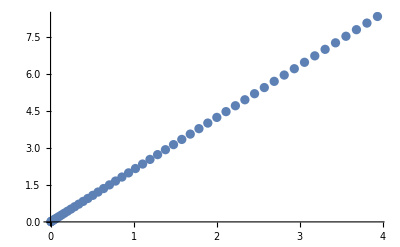

```mathematica
{ωAxis/(4π taap),ωAxis}//Transpose//ListPlot
```

```mathematica
solωRunkZ=SetPrecision[green[kSub]/.psub/.backSub/.{B->bSub,γ->γSub}/.z->zBdr,prec1];
```

To save the normal correlator

```mathematica
SetDirectory[NotebookDirectory[]<>"M_derivative"];
Save["ωcorrμT"<>ToString[100mutilde]<>"d100"<>ToString[10^6 bSub]<>"d10p6",corr1]
```

To save the μ + Δμ correlator

```mathematica
SetDirectory[NotebookDirectory[]<>"M_derivative"];
Save["ωcorrμT"<>ToString[100Round[mutilde]]<>"d100Δ"<>ToString[10^6 bSub]<>"d10p6",corr1]
```

```mathematica
mutilde=100000000001/10000000000
```

100000000001/10000000000

```mathematica
ToString[mutilde//Round]
```

10

### Assuming static M_5 for ω = 0

```mathematica
solω0kZ=SetPrecision[green[kSub]/.psub/.backSub/.{B->bSub,γ->γSub}/.z->zBdr,prec1];
```

```mathematica
solω0kZ//N//MatrixForm
```

(7.29406×10^-17+4.2649×10^-24 ⅈ | 2.97027×10^-30+2.58972×10^-8 ⅈ | 1.14606×10^-6+1.24803×10^-21 ⅈ | -1.38883×10^-24+1.63354×10^-8 ⅈ | 1.92894×10^-17+2.97027×10^-27 ⅈ | 4.2649×10^-21-7.29406×10^-14 ⅈ
-2.97027×10^-30-2.58972×10^-8 ⅈ | 7.29406×10^-17+4.2649×10^-24 ⅈ | 1.38883×10^-24-1.63354×10^-8 ⅈ | 1.14606×10^-6+1.24803×10^-21 ⅈ | -4.2649×10^-21+7.29406×10^-14 ⅈ | 1.92894×10^-17+2.97027×10^-27 ⅈ
-4.78359×10^-18+0. ⅈ | 0.+1.63354×10^-8 ⅈ | 1.94312+0. ⅈ | 0.+1.83182×10^-8 ⅈ | 3.01799×10^-17+0. ⅈ | 0.+4.78359×10^-15 ⅈ
0.-1.63354×10^-8 ⅈ | -4.78359×10^-18+0. ⅈ | 0.-1.83182×10^-8 ⅈ | 1.94312+0. ⅈ | 0.-4.78359×10^-15 ⅈ | 3.01799×10^-17+0. ⅈ
0.+0. ⅈ | 0.-7.29407×10^-14 ⅈ | -2.42419×10^-11+0. ⅈ | 0.+4.78347×10^-15 ⅈ | -1.94312+0. ⅈ | 0.+0. ⅈ
0.+7.29407×10^-14 ⅈ | 0.+0. ⅈ | 0.-4.78347×10^-15 ⅈ | -2.42419×10^-11+0. ⅈ | 0.+0. ⅈ | -1.94312+0. ⅈ)

```mathematica
ⅈ/k solω0kZ⟦1,2⟧/.k->kSub//Re//N
γ μ/.{γ->γSub,μ->mutilde*taap}//N
Solve[%%+n %==0,n]//Flatten
```

-2.58972

1.94229

{n→1.33333}

```mathematica
-ⅈ/k solω0kZ⟦1,4⟧/.k->kSub//N
1/2 γ μ^2/.{γ->γSub,μ->mutilde*taap}//N
```

1.63354+1.38883×10^-16 ⅈ

1.63354

#### Extra

```mathematica
solωΔkZ=SetPrecision[green[kSub]/.psub/.backSub/.{B->bSub,γ->γSub}/.z->zBdr,prec1];
```

```mathematica
ⅈ/k solω0kZ⟦1,2⟧/.k->kSub//Re//N
γ μ/.{γ->γSub,μ->mutilde*taap}//N
Solve[%%+n %==0,n]//Flatten
```

-2.58972

1.94229

{n→1.33333}

```mathematica
-ⅈ/k solω0kZ⟦1,4⟧/.k->kSub//N
1/2 γ μ^2/.{γ->γSub,μ->mutilde*taap}//N
```

1.63354+2.75932×10^-15 ⅈ

1.63354

```mathematica
corr1={kSub,{solω0kZ,solωΔkZ}};
```

```mathematica
"ω0corrμT"<>ToString[100(mutilde-10^-10)]<>"d100"<>ToString[10^6 bSub]<>"d10p6"
```

ω0corrμT1000d1002886d10p6

```mathematica
SetDirectory[NotebookDirectory[]<>"M_derivative"];
Save["ω0corrμT"<>ToString[100100(mutilde-10^-10)]<>"d100"<>ToString[10^6 bSub]<>"d10p6",corr1]
```

#### Transport

### Kubo formula

σ and η are normalized already

Don’t normalize ρ and c’s. If affects the Kubo formula for c’s and η.

#### σ

```mathematica
ρPX[data_,M5μ_]:=bSub[data]^2/(w0[data](w0[data]-bSub[data]^2 M5μ))(all[data]⟦3,3⟧)/ωAxis[data]
ρPTX[data_,M5μ_]:=-bSub[data]^2/(w0[data](w0[data]-bSub[data]^2 M5μ))(all[data]⟦All,3,4⟧)/ωAxis[data]

σPX[data_,M5μ_]:=-1/taap[data] 1/ρPX[data,M5μ]
σPTX[data_,M5μ_]:=-1/taap[data] 1/ρPTX[data,M5μ]
```

#### c

```mathematica
c8X[data_,M5μ_]:=bSub[data]/(w0[data]-bSub[data]^2 M5μ)(ρPX[data,M5μ] all[data]⟦All,3,6⟧+ρPTX[data,M5μ] all[data]⟦All,3,5⟧)/(ωAxis[data](ρPX[data,M5μ]^2+ρPTX[data,M5μ]^2)) 

c10TX[data_,M5μ_]:=bSub[data]/(w0[data]-bSub[data]^2 M5μ)(ρPX[data,M5μ] all[data]⟦All,3,5⟧-ρPTX[data,M5μ]all[data]⟦All,3,6⟧)/(ωAxis[data](ρPX[data,M5μ]^2+ρPTX[data,M5μ]^2)) 


c15X[data_,M5μ_]:=bSub[data]/w0[data](ρPX[data,M5μ] all[data]⟦All,6,3⟧+ρPTX[data,M5μ] all[data]⟦All,5,3⟧)/(ωAxis[data](ρPX[data,M5μ]^2+ρPTX[data,M5μ]^2))  
c17TX[data_,M5μ_]:=bSub[data]/w0[data](ρPX[data,M5μ] all[data]⟦All,5,3⟧-ρPTX[data,M5μ] all[data]⟦All,6,3⟧)/(ωAxis[data](ρPX[data,M5μ]^2+ρPTX[data,M5μ]^2))
```

#### η

```mathematica
ηPX[data_,M5μ_]:=(4π)/entropy[data](all[data]⟦All,5,5⟧)/ωAxis[data] -(c8X[data,M5μ] c15X[data,M5μ]-c10TX[data,M5μ] c17TX[data,M5μ])ρPX[data,M5μ]+(c8X[data,M5μ] c17TX[data,M5μ]+c10TX[data,M5μ] c15X[data,M5μ])ρPTX[data,M5μ] 

ηPTX[data_,M5μ_]:=(4π)/entropy[data](all[data]⟦All,5,6⟧)/ωAxis[data]-(c8X[data,M5μ] c17TX[data,M5μ]+c10TX[data,M5μ] c15X[data,M5μ])ρPX[data,M5μ]-(c8X[data,M5μ] c15X[data,M5μ]-c10TX[data,M5μ] c17TX[data,M5μ])ρPTX[data,M5μ]
```